```mathematica
(* WAHADŁO Z PODWÓJNYM PUNKTEM ZACZEPIENIA *)

(* Równania ruchu w karteziańskim układzie współrzędnych *)
```

```mathematica
deqns={Subscript[m,1] x1''[t]==-(λ2[t]/l) (x2[t]-x1[t]),
Subscript[m,1] y1''[t]==0,
Subscript[m,2] x2''[t]==(λ2[t]/l) (x2[t]-x1[t]),
Subscript[m,2] y2''[t]==(λ2[t]/l) *y2[t]-Subscript[m,2] g}
```

{{{1,x,y},{x,1,z},{y,z,1}}_1 x1''[t]==-((-x1[t]+x2[t]) λ2[t])/l,{{1,x,y},{x,1,z},{y,z,1}}_1 y1''[t]==0,{{1,x,y},{x,1,z},{y,z,1}}_2 x2''[t]==((-x1[t]+x2[t]) λ2[t])/l,{{1,x,y},{x,1,z},{y,z,1}}_2 y2''[t]==-g {{1,x,y},{x,1,z},{y,z,1}}_2+(y2[t] λ2[t])/l}

```mathematica
(* Równania więzów *)
```

```mathematica
aeqns={(x2[t]-x1[t])^2+(y2[t])^2==l^2}
```

{(-x1[t]+x2[t])^2+y2[t]^2==l^2}

```mathematica
(* Warunki początkowe *)
```

```mathematica
ics={x1[0]==0,y1[0]==0,x1'[0]==0,y1'[0]==0,x2[0]==1,y2[0]==0,x2'[0]==0,y2'[0]==0}
```

{x1[0]==0,y1[0]==0,x1'[0]==0,y1'[0]==0,x2[0]==1,y2[0]==0,x2'[0]==0,y2'[0]==0}

```mathematica
(* Parametry układu: grawitacja, masy, długośći nieważkich prętów *)
```

```mathematica
params={g->9.81,Subscript[m,1]->1,Subscript[m,2]->10,l->1}
```

{g→9.81,{{1,x,y},{x,1,z},{y,z,1}}_1→1,{{1,x,y},{x,1,z},{y,z,1}}_2→10,l→1}

```mathematica
(* Rozwiązanie równań różniczkowych z uwzględnieniem więzów, warunków początkowych i wartości parametrów *)
```

```mathematica
soldp=First[NDSolve[{deqns,aeqns,ics}/.params,{x1,y1,x2,y2,λ2},{t,0,15},Method->{"IndexReduction"->{Automatic,"IndexGoal"->0}}]];
```

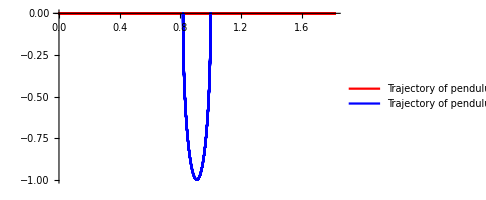

```mathematica
ParametricPlot[Evaluate[{{x1[t],y1[t]},{x2[t],y2[t]}}/.soldp],{t,0,10},PlotStyle->{Red,Blue},ImageSize->Medium,PlotLegends->{"Trajectory of pendulum 1","Trajectory of pendulum 2"}]
```

```mathematica
Animate[Graphics[{{PointSize[.025],{Red,Point[{x1[t],y1[t]}]},{Blue,Point[{x2[t],y2[t]}]},Line[{{0,0},{x1[t],y1[t]},{x2[t],y2[t]}}]}/.soldp,{Gray,Line[Map[Function[Evaluate[{x2[#],y2[#]}/.soldp]],Range[0,t,0.025]]]}},PlotRange->{{-2,2},{-2,0}},Axes->True,Ticks->False,ImageSize->500],{t,0,10,.025},SaveDefinitions->True]
```

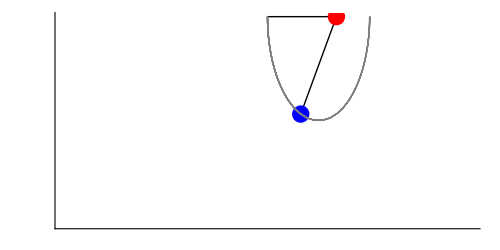

```mathematica
With[{t=3.7},Graphics[{{Thick,Line[{{0,0},{x1[t],y1[t]},{x2[t],y2[t]}}],PointSize[.025],{Red,Point[{x1[t],y1[t]}]},{Blue,Point[{x2[t],y2[t]}]},}/.soldp,{Gray,Line[Map[Function[Evaluate[{x2[#],y2[#]}/.soldp]],Range[0,t,0.025]]]}},PlotRange->{{-2,2},{-2,0}},Axes->True,Ticks->False,ImageSize->500]]
```